6

{1.,1.1,1.2,1.3,1.4,1.5}

{0,-0.111502,-0.253884,-0.445626,-0.722859,-1.16778}

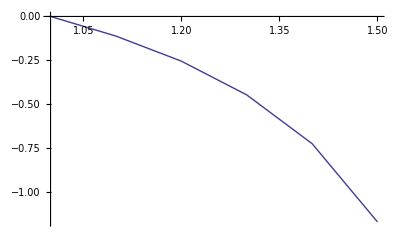

```mathematica
f[x_,y_]:=-(x^2 y^2-(2x+1)y + 1)/x;
y0=0;
a=1;
b=1.5;
h=0.1;
X=Range[a,b,h];
n=Length[X];
Print[n];
Print[X];
Y=Table[{},{n}];
Y[[1]]=y0;
For[i=2,i≤n,i++,
K1 = h f[X[[i-1]],Y[[i-1]]];
K2 =  h f[X[[i-1]] + h/2,Y[[i-1]] + K1/2];
K3 =  h f[X[[i-1]] + h/2,Y[[i-1]] + K2/2];
K4 =  h f[X[[i-1]] + h,Y[[i-1]] + K3];
delta = 1/6(K1 + 2 K2 + 2 K3 + K4);
Y[[i]]=Y[[i-1]]+delta;
];
Print[Y];
dots=Table[{},{n}];
For[i=1,i≤n,i++,
dots[[i]]={X[[i]],Y[[i]]};
]
ListLinePlot[dots]
```